## Sample crediblePlot notebook

### Import crediblePlot

I suggest you place crediblePlot in a path known to mathematica, you can check the paths mathematica searches using:

```mathematica
$Path
```

{/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Links,/home/jay/.Mathematica/Kernel,/home/jay/.Mathematica/Autoload,/home/jay/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/jay,/usr/local/Wolfram/Mathematica/11.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/11.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/11.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/11.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/11.0/Documentation/English/System,/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Data/ICC,/home/jay/Physics/Codes/CrediblePlot}

use one of the above folders, or add the folder where you keep crediblePlot with (replace with your directory first):

```mathematica
userPath="/home/jay/Physics/Codes/CrediblePlot";
```

```mathematica
If[ValueQ[userPath],Import[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}],"Text"]<>"\n\nAppendTo[$Path,\""<>userPath<>"\"];"//Export[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}],#,"Text"]&;Exit[];,Print["Please set userPath first"];];
```

You can now load crediblePlot in any notebook (skipping the above) via:

```mathematica
<<"crediblePlot.m"
```

Welcome to crediblePlot, the available functions are: CrediblePlot1D, LogCrediblePlot1D, CrediblePlot2D and LogLogCrediblePlot2D. See the github page or readme for more details.

### Generate some fake data

CrediblePlot will take probability samples **not probabilitiyUsing a bivariate gaussian distribution with no covariance:

```mathematica
f[x_,y_]:= PDF[NormalDistribution[5,1],x]PDF[NormalDistribution[5,1],y];
```

```mathematica
data=ParallelTable[x=RandomReal[10];y=RandomReal[10];{x,y,f[x,y]},{n,1,10^5}];
```

Normalize the data:

```mathematica
data[[All,3]]/=Plus@@data[[All,3]];
```

### The 1D marginal posteriors

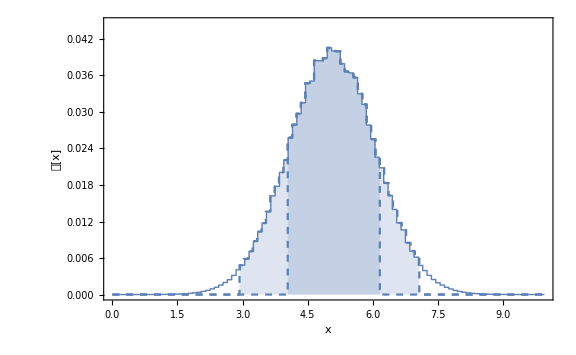
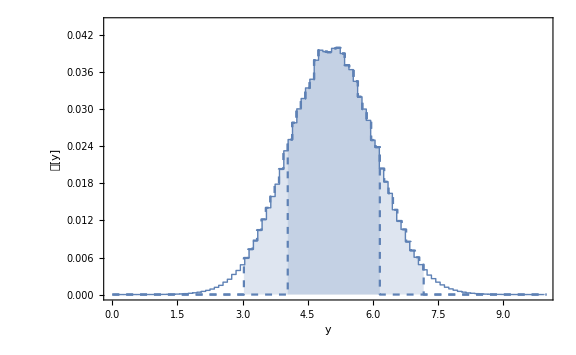

```mathematica
{CrediblePlot1D[data[[All,{1,3}]],100,FrameLabel->{"x","𝒫[x]"}],CrediblePlot1D[data[[All,{2,3}]],100,FrameLabel->{"y","𝒫[y]"}]}
```

```mathematica
LogCrediblePlot1D[data[[All,{2,3}]],100,FrameLabel->{"y","𝒫[y]"}]
```

$Aborted

### The 2D marginal posterior

Credible regions are shaded by default, smoothing is off by default:

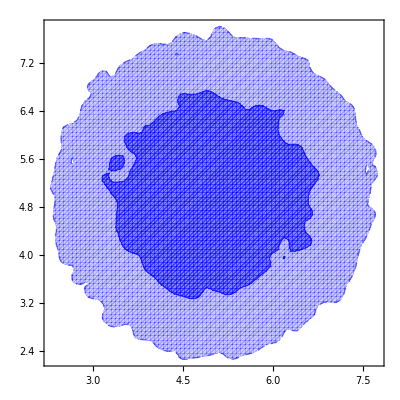
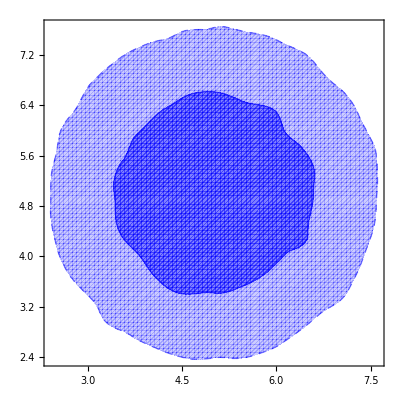

```mathematica
{CrediblePlot2D[data,50],CrediblePlot2D[data,50,Smoothing->True]}
```

You can choose to show the density instead of shading:

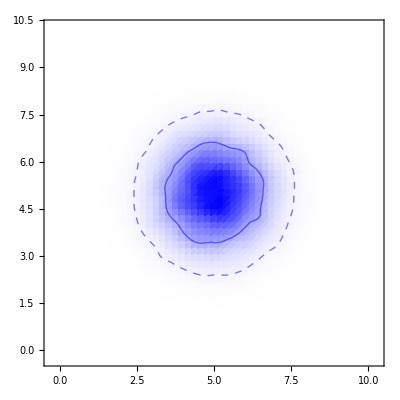

```mathematica
CrediblePlot2D[data,50,Smoothing->True,ShowDensity->True]
```